```mathematica
Get["Aperture/ApertureDefinition.m"]
```

```mathematica
CloseKernels[];
```

```mathematica
LaunchKernels[1]
```

{KernelObject[1,local]}

```mathematica
Length[Flatten[Table[1,{x0,0.025-0.02,0.025+0.02,0.005},{y0,-0.04,0.04,0.01},{th,0,Pi/4,Pi/4/10},{p,0,1187000,1187000/10}]]]
```

9801

```mathematica
9*9*11*11
```

9801

```mathematica
ApertTable=Table[
AbsoluteTiming[
Table[ApertureFunc[0.01,0.035,0.025,0.,x0,y0,th,p,0.2,prec],
{x0,0.025-0.02,0.025+0.02,0.005},{y0,-0.04,0.04,0.01},{th,0,Pi/4,Pi/4/10},{p,0,1187000,1187000/10}]
],
{prec,1,4}];
```

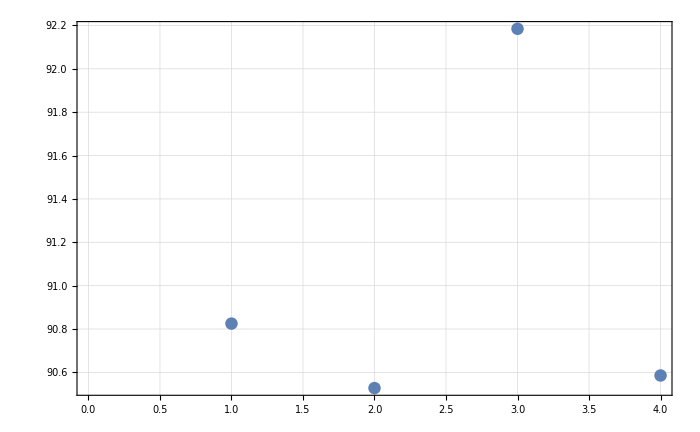

```mathematica
ListPlot[Table[(Table[ApertureFunc[0.01,0.035,0.025,0.,x0,y0,th,p,0.2,prec],{x0,0.025-0.02,0.025+0.02,0.005},{y0,-0.04,0.04,0.01},{th,0,Pi/4,Pi/4/10},{p,0,1187000,1187000/10}]//AbsoluteTiming)[[1]],{prec,1,4}]]
```

```mathematica
MCTable=Table[{
steps,
AbsoluteTiming[Table[MonteCarloAperture[0.01,0.035,0.025,0.,x0,y0,th,p,0.2,steps],
{x0,0.025-0.02,0.025+0.02,0.005},{y0,-0.04,0.04,0.01},{th,0,Pi/4,Pi/4/10},{p,0,1187000,1187000/10}]]
},{steps,100,2100,500}];
```

```mathematica
MCTable//Dimensions
```

{5,2}

```mathematica
MCTable[[1,2,2]]//Dimensions
```

{9,9,11,11}

```mathematica
ApertTable[[1,2]]//Dimensions
```

{9,9,11,11}

```mathematica
RelCompareList=If[#[[2]]==0,0.,(#[[1]]-#[[2]])/#[[2]]]&/@Transpose[{Flatten[MCTable[[1,2,2]]],Re[Flatten[ApertTable[[4,2]]]]}];
```

```mathematica
CleanList=Cases[RelCompareList,_?(#≠0&)];
```

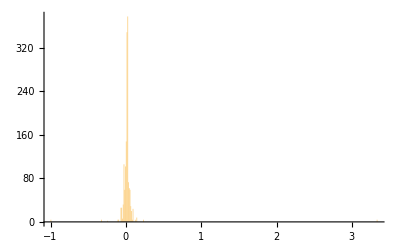

```mathematica
Histogram[CleanList,PlotRange->All(*{{-0.04,0.04},All}*)]
```

```mathematica
RelCompareList2=If[#[[2]]==0,0.,(#[[1]]-#[[2]])/#[[2]]]&/@Transpose[{Flatten[MCTable[[2,2,2]]],Re[Flatten[ApertTable[[4,2]]]]}];
```

```mathematica
CleanList2=Cases[RelCompareList2,_?(#≠0&)];
```

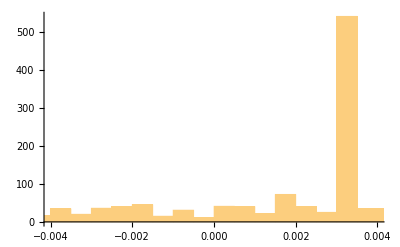

```mathematica
Histogram[CleanList2,2000,PlotRange->{{-0.004,0.004},All}]
```

```mathematica
Mean[CleanList]
```

0.0197455

```mathematica
StandardDeviation[CleanList]
```

0.181086

```mathematica
Mean[CleanList2]
```

-0.00127203

```mathematica
StandardDeviation[CleanList2]
```

0.0536427

```mathematica
Table[StandardDeviation[Flatten[MCTable[[jj,2,2]]-ApertTable[[iii,2]]]],{jj,1,5},{iii,1,4}]
```

{{0.00570788,0.00325567,0.00296841,0.00296841},{0.00369103,0.00084989,0.000486654,0.000486657},{0.00352068,0.000650669,0.000275692,0.000275692},{0.00346295,0.000579832,0.000187808,0.00018781},{0.00343729,0.000549525,0.000143814,0.000143818}}

```mathematica
Table[StandardDeviation[Flatten[MCTable[[jj,2,2]]-ApertTable[[iii,2]]]],{jj,1,5},{iii,1,4}]/Table[Re[Mean[Flatten[MCTable[[jj,2,2]]-ApertTable[[iii,2]]]]],{jj,1,5},{iii,1,4}]
```

{{3.47046,3.99207,4.30571,4.30569},{3.43775,3.47596,4.11089,4.1108},{3.4482,3.39153,4.19446,4.19423},{3.47803,3.4826,4.65206,4.65172},{3.47829,3.45521,4.36874,4.36838}}

### took 364s

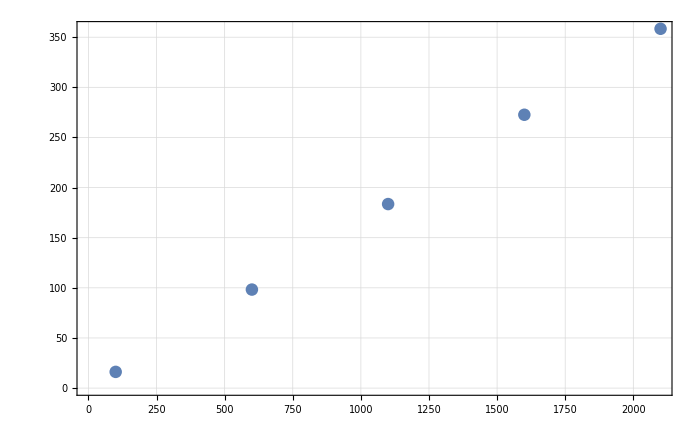

```mathematica
ListPlot[]
```

### took 929s

new method

```mathematica
IntersectionAngles[x_]:=Piecewise[
{
(*{{0,2*Pi},x===ComplexInfinity},*)
{{0,0},x≤-1},
{{0,2π},x≥1},
{{ArcCos[x],2π-ArcCos[x]},True}
}
];

IntervalMod[{min_,max_}]:=Interval@@Piecewise[
{
{{{0,max-2π},{min,2π}},min≤2π≤max},
{{Mod[{min,max},2π]},True}
}];

CircleInRectangle2[xA_,yA_,xOff_,yOff_,xGC_,yGC_,r_]:=
Piecewise[(*we need a piecewise for r=0*)
{
{1,r==0&&-xA/2+xOff≤xGC≤xA/2+xOff&&-yA/2+yOff≤yGC≤yA/2+yOff},
{0,r==0(*&&(-xA/2+xOff>xGC||xA/2+xOff<xGC)&&(-yA/2+yOff>yGC||yA/2+yOff<yGC)*)}(*this is sufficient as it will first check first case, then second, so it has to be outside in this case*)
},
Module[{arr={xOff-xGC+xA/2,yOff-yGC+yA/2,-(xOff-xGC-xA/2),-(yOff-yGC-yA/2)}/r,int},
(*{arr,
Table[IntersectionAngles[arr[[i]]]+(i-1)π/2,{i,4}],
Table[IntervalMod[IntersectionAngles[arr[[i]]]+(i-1)π/2],{i,4}],*)
int=IntervalIntersection@@Table[IntervalMod[IntersectionAngles[arr[[i]]]+(i-1)π/2],{i,4}];
 RegionMeasure[int,1]/(2Pi)(*,
r RegionMeasure[int]
}*)
]
]
```

```mathematica
ArithCircleTable=Table[CircleInRectangle2[0.01,0.035,0.025,0.,x0,y0,rG[p,th,0.2]],{x0,0.025-0.02,0.025+0.02,0.005},{y0,-0.04,0.04,0.01},{th,0,Pi/4,Pi/4/10},{p,0,1187000,1187000/10}]
```

{{{{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0}},7,{{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0}}},7,{{{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},6,{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0}},8}}
 |  |  |  |

```mathematica
RelCompareList3=If[#[[2]]==0,0.,(#[[1]]-#[[2]])/#[[2]]]&/@Transpose[{Flatten[ArithCircleTable],Re[Flatten[ApertTable[[4,2]]]]}];
```

```mathematica
CleanList3=Cases[RelCompareList3,_?(#≠0&)];
```

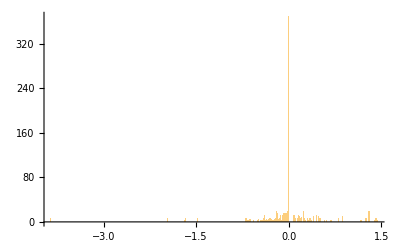

```mathematica
Histogram[CleanList3,2000,PlotRange->All(*{{-0.004,0.004},All}*)]
```

```mathematica
Mean[CleanList3]
```

4.6103×10^-10

```mathematica
Min[Flatten[Re[ApertTable[[4,2]]]-ArithCircleTable]]
```

-6.52206×10^-8

```mathematica
Mean[Flatten[Re[ApertTable[[4,2]]]-ArithCircleTable]]
```

4.15484×10^-11

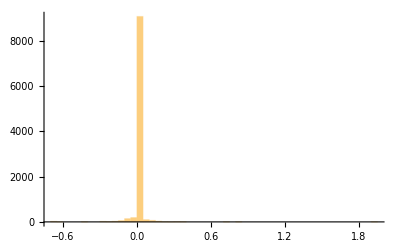

```mathematica
Histogram[Flatten[Re[ApertTable[[4,2]]]-ArithCircleTable],50,PlotRange->All]
```

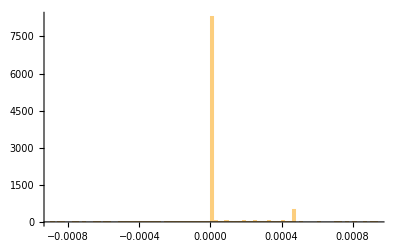

```mathematica
Histogram[Flatten[MCTable[[5,2,2]]-ArithCircleTable],100,PlotRange->All]
```

```mathematica
ApertTable//Dimensions
```

{4,2}

```mathematica
Mean[Flatten[Re[ApertTable[[1,2]]]-Re[ApertTable[[4,2]]]]]
```

-0.00095529

```mathematica
ArithCircleTable[[1,4,2,2]]
```

0

```mathematica
ApertTable[[1,2,1,4,2,2]]
```

0.

```mathematica
{{x0,0.025-0.02},{y0,-0.04+4*0.01},{th,Pi/4/10},{p,1187000/10}}
```

{{x0,0.005},{y0,0.},{th,π/40},{p,118700}}

```mathematica
ApertureFunc[0.01,0.035,0.025,0.,0.005,0.,Pi/40,118700,0.2,4]
```

0.

```mathematica
CircleInRectangle[0.01,0.035,0.025,0.,0.005,0.,rG[118700,Pi/40,0.2]]
```

ImplicitRegion[0.02≤x≤0.03&&-0.0175≤y≤0.0175&&{x,y}∈Circle[{0.005,0.},0.000155326],{x,y}]

```mathematica
1/(2.*Pi)
```

0.159155

```mathematica
(Re[ApertTable[[4,2]]]-ArithCircleTable)[[All,4;;5]]//TableForm
```

0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -7.16363×10^-9
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -1.35803×10^-8 | -6.76392×10^-9
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | 3.33067×10^-15 | 3.29207×10^-8 | 1.29788×10^-8
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -7.12559×10^-9 | -1.76525×10^-14 | 1.44309×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -7.16363×10^-9
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -1.35803×10^-8 | -6.76392×10^-9
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | 3.33067×10^-15 | 3.29207×10^-8 | 1.05286×10^-8
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -7.12559×10^-9 | 9.32587×10^-15 | 7.1493×10^-9
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -1.94183×10^-8 | 2.40363×10^-14
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -7.41649×10^-9 | -2.7256×10^-8 | -8.70633×10^-9 | 1.55331×10^-8
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -1.74851×10^-8 | -5.96467×10^-14 | -8.22541×10^-9 | 3.4861×10^-14 | 8.94535×10^-9
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -1.15028×10^-8 | 1.32198×10^-8 | -4.9604×10^-9 | 9.6978×10^-14 | 9.21253×10^-9 | -6.83897×10^-14
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | 2.87858×10^-8 | 7.21734×10^-9 | -7.1896×10^-9 | -2.44804×10^-14 | 4.40759×10^-14 | 1.48215×10^-14
0. | -0.159155 | -0.159155 | -0.159155 | -7.66193×10^-14 | -5.84219×10^-9 | 5.18862×10^-9 | 8.91344×10^-9 | 1.02377×10^-8 | 1.94289×10^-15 | 2.58682×10^-13
0. | -0.159155 | -0.159155 | -0.159155 | -2.13537×10^-8 | -5.18802×10^-9 | 6.36158×10^-14 | -6.40199×10^-9 | -8.32667×10^-16 | 1.26785×10^-8 | 7.63012×10^-12 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -1.94183×10^-8 | 2.40363×10^-14
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -7.41649×10^-9 | -2.7256×10^-8 | -8.70633×10^-9 | 1.55331×10^-8
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -1.74851×10^-8 | -5.96467×10^-14 | -8.22541×10^-9 | 3.4861×10^-14 | 8.94535×10^-9
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -1.15028×10^-8 | 1.32198×10^-8 | -4.9604×10^-9 | 9.6978×10^-14 | 8.18245×10^-9 | -3.35842×10^-14
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | 2.87858×10^-8 | 7.21734×10^-9 | -7.1896×10^-9 | 3.58602×10^-14 | -1.9984×10^-14 | 2.70339×10^-14
0. | -0.159155 | -0.159155 | -0.159155 | -7.66193×10^-14 | -5.84219×10^-9 | 5.18862×10^-9 | 8.91344×10^-9 | 6.5019×10^-9 | 6.82787×10^-15 | 1.05471×10^-14
0. | -0.159155 | -0.159155 | -0.159155 | -2.13537×10^-8 | -5.18802×10^-9 | 6.36158×10^-14 | -5.92774×10^-9 | 2.85327×10^-14 | 4.32274×10^-9 | 5.55112×10^-17
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -6.26568×10^-8 | -4.03281×10^-8 | -2.5056×10^-8 | 3.86708×10^-9 | 1.92919×10^-7 | -6.50123×10^-8 | -1.22642×10^-8 | 3.86564×10^-9 | 3.46852×10^-8 | -1.71235×10^-8
0 | -6.50774×10^-8 | -6.50804×10^-8 | -6.52206×10^-8 | -1.79316×10^-8 | -1.17×10^-8 | -8.26901×10^-9 | 2.06168×10^-13 | 9.90671×10^-9 | 1.48751×10^-8 | 1.96155×10^-8
0 | -2.24445×10^-8 | -2.24444×10^-8 | 3.52629×10^-8 | 9.97694×10^-9 | -5.58997×10^-14 | -1.02854×10^-8 | -9.17529×10^-9 | 9.97739×10^-9 | 4.92742×10^-9 | 1.94067×10^-13
0 | -2.90014×10^-8 | 1.00767×10^-8 | -1.53437×10^-8 | 1.00767×10^-8 | -7.0502×10^-9 | 2.20272×10^-9 | 2.78222×10^-13 | -8.34666×10^-9 | 2.83107×10^-14 | 7.44437×10^-9
0 | -1.18845×10^-8 | -1.18837×10^-8 | -1.18835×10^-8 | 2.03033×10^-8 | -1.01031×10^-8 | 4.36893×10^-9 | 3.53326×10^-9 | 1.2057×10^-13 | 1.51434×10^-13 | 4.44644×10^-14
0 | -2.55425×10^-8 | -3.04923×10^-13 | 1.56207×10^-8 | 1.51767×10^-13 | -8.89872×10^-9 | -4.59742×10^-9 | 7.16967×10^-9 | -9.12603×10^-14 | -6.43776×10^-9 | -5.51226×10^-14
0 | 7.38351×10^-8 | -1.2706×10^-8 | -4.14567×10^-9 | 4.96252×10^-9 | -4.7426×10^-9 | -4.14558×10^-9 | 2.24978×10^-9 | -6.45762×10^-9 | -2.83107×10^-15 | 9.89692×10^-9
0 | 1.95551×10^-8 | 1.95551×10^-8 | 1.07997×10^-8 | -5.13143×10^-9 | -4.3463×10^-9 | -3.80657×10^-9 | -4.7462×10^-14 | 9.21197×10^-9 | 1.5189×10^-9 | 1.33929×10^-11
0 | -8.03983×10^-9 | -8.04027×10^-9 | 9.41501×10^-9 | 9.41513×10^-9 | 2.68594×10^-9 | -3.76106×10^-9 | 9.89209×10^-14 | 5.71159×10^-10 | 1.14377×10^-11 | 2.65356×10^-11
0 | 8.33141×10^-8 | -4.47102×10^-9 | 4.86436×10^-9 | -4.47077×10^-9 | 2.36818×10^-9 | -6.46469×10^-9 | 2.61458×10^-14 | 4.35699×10^-12 | 6.12776×10^-11 | 1.0455×10^-12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -6.26568×10^-8 | -4.03281×10^-8 | -2.5056×10^-8 | 3.86708×10^-9 | 1.92919×10^-7 | -6.50123×10^-8 | -1.22642×10^-8 | 3.86564×10^-9 | 3.46852×10^-8 | -1.71235×10^-8
0 | -6.50774×10^-8 | -6.50804×10^-8 | -6.52206×10^-8 | -1.79316×10^-8 | -1.17×10^-8 | -8.26901×10^-9 | 2.06168×10^-13 | 9.90671×10^-9 | 1.48751×10^-8 | 1.96155×10^-8
0 | -2.24445×10^-8 | -2.24444×10^-8 | 3.52629×10^-8 | 9.97694×10^-9 | -5.58997×10^-14 | -1.02854×10^-8 | -9.17529×10^-9 | 9.97739×10^-9 | 4.92742×10^-9 | 1.94067×10^-13
0 | -2.90014×10^-8 | 1.00767×10^-8 | -1.53437×10^-8 | 1.00767×10^-8 | -7.0502×10^-9 | 2.20272×10^-9 | 2.78222×10^-13 | -8.34666×10^-9 | 2.83107×10^-14 | 7.44437×10^-9
0 | -1.18845×10^-8 | -1.18837×10^-8 | -1.18835×10^-8 | 2.03033×10^-8 | -1.01031×10^-8 | 4.36893×10^-9 | 3.53326×10^-9 | 1.2057×10^-13 | 1.51434×10^-13 | -2.7256×10^-14
0 | -2.55425×10^-8 | -3.04923×10^-13 | 1.56207×10^-8 | 1.51767×10^-13 | -8.89872×10^-9 | -4.59742×10^-9 | 7.16967×10^-9 | -9.12603×10^-14 | -5.70429×10^-9 | -2.81997×10^-14
0 | 7.38351×10^-8 | -1.2706×10^-8 | -4.14567×10^-9 | 4.96252×10^-9 | -4.7426×10^-9 | -4.14558×10^-9 | 2.24978×10^-9 | -5.60699×10^-9 | -6.4948×10^-14 | 7.74707×10^-9
0 | 1.95551×10^-8 | 1.95551×10^-8 | 1.07997×10^-8 | -5.13143×10^-9 | -4.3463×10^-9 | -3.80657×10^-9 | -1.80411×10^-14 | 4.22989×10^-9 | 8.55277×10^-10 | 4.58611×10^-9
0 | -8.03983×10^-9 | -8.04027×10^-9 | 9.41501×10^-9 | 9.41513×10^-9 | 2.68594×10^-9 | -3.5454×10^-9 | 8.9373×10^-14 | 1.20644×10^-8 | 6.07869×10^-9 | 5.3071×10^-11
0 | 8.33141×10^-8 | -4.47102×10^-9 | 4.86436×10^-9 | -4.47077×10^-9 | 2.36818×10^-9 | -5.54427×10^-9 | -9.59233×10^-14 | 1.81131×10^-10 | 1.22555×10^-10 | 2.09083×10^-12
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.41356×10^-9 | 8.67036×10^-10
0 | 0. | 0. | 0. | 0. | 0. | 0. | 2.3667×10^-8 | 1.31763×10^-9 | 5.63764×10^-9 | 1.54876×10^-14
0 | 0. | 0. | 0. | 0. | 0. | 8.95547×10^-9 | 2.58574×10^-10 | 1.32831×10^-9 | 2.22045×10^-16 | 2.14598×10^-12
0 | 0. | 0. | 0. | 0. | 1.54941×10^-8 | 4.61623×10^-10 | 1.10278×10^-9 | 5.71765×10^-15 | 1.18924×10^-12 | 1.11716×10^-13
0 | 0. | 0. | 0. | 0. | 9.17222×10^-9 | 2.9324×10^-9 | 7.21645×10^-16 | 1.19019×10^-12 | 8.51819×10^-14 | 8.82627×10^-15
0 | 0. | 0. | 0. | 3.60531×10^-8 | 1.06142×10^-10 | 8.88178×10^-16 | 2.30732×10^-12 | 1.26538×10^-13 | 9.79772×10^-15 | 1.22125×10^-15
0 | 0. | 0. | 0. | 1.76071×10^-8 | 2.73935×10^-9 | 2.30926×10^-14 | 3.72119×10^-13 | 2.00673×10^-14 | 1.77636×10^-15 | 2.498×10^-16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.41356×10^-9 | 8.67036×10^-10
0 | 0. | 0. | 0. | 0. | 0. | 0. | 2.3667×10^-8 | 1.31763×10^-9 | 5.63764×10^-9 | 3.40037×10^-10
0 | 0. | 0. | 0. | 0. | 0. | 8.95547×10^-9 | 2.58574×10^-10 | 1.32831×10^-9 | 6.6029×10^-11 | 5.35472×10^-12
0 | 0. | 0. | 0. | 0. | 1.54941×10^-8 | 4.61623×10^-10 | 1.10278×10^-9 | 3.79264×10^-11 | 2.37815×10^-12 | 2.23377×10^-13
0 | 0. | 0. | 0. | 0. | 9.17222×10^-9 | 2.9324×10^-9 | 5.56753×10^-11 | 2.38032×10^-12 | 1.70253×10^-13 | 1.75415×10^-14
0 | 0. | 0. | 0. | 3.60531×10^-8 | 1.06142×10^-10 | 2.14756×10^-10 | 5.18668×10^-12 | 2.52853×10^-13 | 1.93734×10^-14 | 2.27596×10^-15
0 | 0. | 0. | 0. | 1.76071×10^-8 | 2.73935×10^-9 | 2.64966×10^-11 | 7.44016×10^-13 | 3.9857×10^-14 | 3.38618×10^-15 | 2.22045×10^-16
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -6.26469×10^-8 | -4.03324×10^-8 | -2.50581×10^-8 | 3.86511×10^-9 | 1.92916×10^-7 | -6.50126×10^-8 | -1.22651×10^-8 | 3.86576×10^-9 | 3.46866×10^-8 | -1.7124×10^-8
0 | -6.50779×10^-8 | -6.50769×10^-8 | -6.52189×10^-8 | -1.79305×10^-8 | -1.16994×10^-8 | -8.26836×10^-9 | 2.8022×10^-13 | 9.90668×10^-9 | 1.48753×10^-8 | 1.96156×10^-8
0 | -2.24478×10^-8 | -2.24434×10^-8 | 3.52623×10^-8 | 9.97741×10^-9 | 8.42659×10^-14 | -1.02855×10^-8 | -9.17485×10^-9 | 9.97707×10^-9 | 4.9274×10^-9 | -6.82232×10^-14
0 | -2.89985×10^-8 | 1.00777×10^-8 | -1.53437×10^-8 | 1.00766×10^-8 | -7.05021×10^-9 | 2.20342×10^-9 | -2.4869×10^-14 | -8.34647×10^-9 | -1.04916×10^-13 | 7.44446×10^-9
0 | -1.18832×10^-8 | -1.18833×10^-8 | -1.18836×10^-8 | 2.03033×10^-8 | -1.01035×10^-8 | 4.36879×10^-9 | 3.53351×10^-9 | 2.30704×10^-13 | -1.14131×10^-13 | -1.14297×10^-13
0 | -2.55439×10^-8 | 2.78444×10^-13 | 1.5621×10^-8 | 2.74447×10^-13 | -8.89872×10^-9 | -4.59741×10^-9 | 7.1696×10^-9 | -6.45595×10^-14 | -6.43787×10^-9 | 2.00395×10^-14
0 | 7.38359×10^-8 | -1.27062×10^-8 | -4.14551×10^-9 | 4.96274×10^-9 | -4.74236×10^-9 | -4.14559×10^-9 | 2.24994×10^-9 | -6.45754×10^-9 | -3.33067×10^-14 | 9.89692×10^-9
0 | 1.95539×10^-8 | 1.95549×10^-8 | 1.08×10^-8 | -5.13144×10^-9 | -4.3466×10^-9 | -3.80658×10^-9 | -2.9754×10^-14 | 9.21213×10^-9 | 1.5189×10^-9 | 1.3393×10^-11
0 | -8.03926×10^-9 | -8.04008×10^-9 | 9.41511×10^-9 | 9.41519×10^-9 | 2.68592×10^-9 | -3.7611×10^-9 | 4.60187×10^-14 | 5.7116×10^-10 | 1.1438×10^-11 | 2.65355×10^-11
0 | 8.33141×10^-8 | -4.47118×10^-9 | 4.8637×10^-9 | -4.47095×10^-9 | 2.36821×10^-9 | -6.46482×10^-9 | -1.03917×10^-13 | 4.35676×10^-12 | 6.12775×10^-11 | 1.04561×10^-12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -6.26469×10^-8 | -4.03324×10^-8 | -2.50581×10^-8 | 3.86511×10^-9 | 1.92916×10^-7 | -6.50126×10^-8 | -1.22651×10^-8 | 3.86576×10^-9 | 3.46866×10^-8 | -1.7124×10^-8
0 | -6.50779×10^-8 | -6.50769×10^-8 | -6.52189×10^-8 | -1.79305×10^-8 | -1.16994×10^-8 | -8.26836×10^-9 | 2.8022×10^-13 | 9.90668×10^-9 | 1.48753×10^-8 | 1.96156×10^-8
0 | -2.24478×10^-8 | -2.24434×10^-8 | 3.52623×10^-8 | 9.97741×10^-9 | 8.42659×10^-14 | -1.02855×10^-8 | -9.17485×10^-9 | 9.97707×10^-9 | 4.9274×10^-9 | -6.82232×10^-14
0 | -2.89985×10^-8 | 1.00777×10^-8 | -1.53437×10^-8 | 1.00766×10^-8 | -7.05021×10^-9 | 2.20342×10^-9 | -2.4869×10^-14 | -8.34647×10^-9 | -1.04916×10^-13 | 7.44446×10^-9
0 | -1.18832×10^-8 | -1.18833×10^-8 | -1.18836×10^-8 | 2.03033×10^-8 | -1.01035×10^-8 | 4.36879×10^-9 | 3.53351×10^-9 | 2.30704×10^-13 | -1.14131×10^-13 | -5.10147×10^-14
0 | -2.55439×10^-8 | 2.78444×10^-13 | 1.5621×10^-8 | 2.74447×10^-13 | -8.89872×10^-9 | -4.59741×10^-9 | 7.1696×10^-9 | -6.45595×10^-14 | -5.70422×10^-9 | -5.22915×10^-14
0 | 7.38359×10^-8 | -1.27062×10^-8 | -4.14551×10^-9 | 4.96274×10^-9 | -4.74236×10^-9 | -4.14559×10^-9 | 2.24994×10^-9 | -5.60693×10^-9 | -4.19109×10^-14 | 7.74707×10^-9
0 | 1.95539×10^-8 | 1.95549×10^-8 | 1.08×10^-8 | -5.13144×10^-9 | -4.3466×10^-9 | -3.80658×10^-9 | -2.65898×10^-14 | 4.22994×10^-9 | 8.55278×10^-10 | 4.58611×10^-9
0 | -8.03926×10^-9 | -8.04008×10^-9 | 9.41511×10^-9 | 9.41519×10^-9 | 2.68592×10^-9 | -3.5452×10^-9 | 1.53211×10^-14 | 1.20644×10^-8 | 6.07869×10^-9 | 5.30709×10^-11
0 | 8.33141×10^-8 | -4.47118×10^-9 | 4.8637×10^-9 | -4.47095×10^-9 | 2.36821×10^-9 | -5.54428×10^-9 | 4.88498×10^-15 | 1.8113×10^-10 | 1.22555×10^-10 | 2.09099×10^-12
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | 1.17462×10^-13 | -9.69042×10^-9
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -1.54004×10^-8 | 1.33504×10^-14 | -3.4972×10^-14 | -1.68199×10^-14
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -7.3895×10^-9 | -9.44676×10^-9 | -2.7367×10^-14 | 1.21718×10^-8 | -2.15106×10^-13
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -7.16382×10^-9 | -6.15066×10^-9 | 6.33292×10^-9 | 1.13114×10^-8 | 4.13003×10^-14 | -6.3467×10^-9
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -6.76355×10^-9 | -5.20556×10^-9 | -1.1352×10^-13 | -6.44211×10^-9 | 1.04281×10^-8 | -6.19492×10^-9
0. | -0.159155 | -0.159155 | -0.159155 | -8.81033×10^-9 | 1.05286×10^-8 | -4.57845×10^-9 | 1.20792×10^-13 | -8.42104×10^-14 | 1.15557×10^-8 | 1.2979×10^-8
0. | -0.159155 | -0.159155 | -0.159155 | -7.12556×10^-9 | 7.1493×10^-9 | 1.08074×10^-8 | -9.49241×10^-15 | -6.24825×10^-9 | 7.78821×10^-14 | 1.44385×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | 1.17462×10^-13 | -9.69042×10^-9
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -1.54004×10^-8 | 1.33504×10^-14 | -3.4972×10^-14 | -1.68199×10^-14
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -7.3895×10^-9 | -9.44676×10^-9 | -2.7367×10^-14 | 1.21718×10^-8 | -2.15106×10^-13
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -7.16382×10^-9 | -6.15066×10^-9 | 6.33292×10^-9 | 1.13114×10^-8 | -6.01186×10^-14 | -5.61401×10^-9
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -6.76355×10^-9 | -5.20556×10^-9 | -1.1352×10^-13 | -6.24716×10^-9 | 6.25421×10^-9 | -5.00527×10^-9
0. | -0.159155 | -0.159155 | -0.159155 | -8.81033×10^-9 | 1.05286×10^-8 | -4.57845×10^-9 | 1.20792×10^-13 | -5.29021×10^-14 | 5.09644×10^-9 | 4.15999×10^-9
0. | -0.159155 | -0.159155 | -0.159155 | -7.12556×10^-9 | 7.1493×10^-9 | 1.08074×10^-8 | 1.80966×10^-14 | -5.193×10^-9 | -2.4758×10^-14 | 3.55184×10^-9
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -7.16364×10^-9
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -1.35804×10^-8 | -6.76398×10^-9
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | 2.86438×10^-14 | 3.29207×10^-8 | 1.29788×10^-8
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -7.12565×10^-9 | 4.29101×10^-14 | 1.44309×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -7.16364×10^-9
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -1.35804×10^-8 | -6.76398×10^-9
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | 2.86438×10^-14 | 3.29207×10^-8 | 1.05286×10^-8
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -7.12565×10^-9 | 8.04912×10^-16 | 7.14948×10^-9
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155
0. | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155 | -0.159155